```mathematica
StickerPack[n_/;n>0,m_/;m>0]:=RandomSample[Range[m],n]
```

```mathematica
BuyPack[collection_,n_,m_]:=Module[{Pack,found},
Pack=StickerPack[n,m];
found=Normal@SparseArray[Pack->ConstantArray[True,n],{m},False];
Thread[collection∨found]
]
```

```mathematica
CouponProblem[n_,m_,True]:=NestWhileList[
		BuyPack[#,n,m]&,ConstantArray[False,m],
	!AllTrue[#,TrueQ]&]
```

```mathematica
CouponProblem[n_,m_]:=(CouponProblem[n,m,True]//Dimensions//Part[#,1]&)-1
```

```mathematica
dd=Table[CouponProblem[n,400],{30},{n,400}]//N//Mean;
```

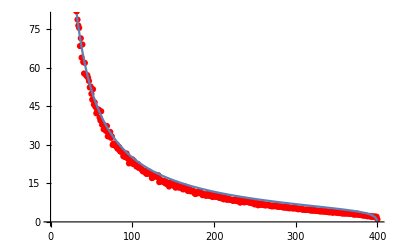

```mathematica
Show[ListPlot[dd,PlotStyle->Red],ListLinePlot[Table[400/(i)*HarmonicNumber[400-i],{i,400.}]]]
```

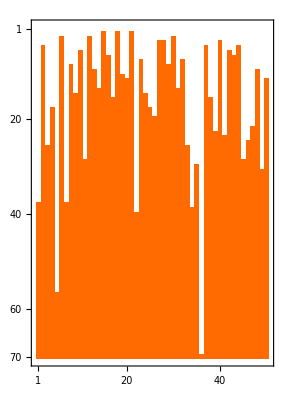

```mathematica
CouponProblem[3,50,True]//Boole//MatrixPlot
```

```mathematica
400/(i)*HarmonicNumber[400-i]/.i->8.
```

327.488